# PHAS2443: Practical Mathematics II Exercises 4: Time-Dependent Problems Model Solutions

1. We saw in Lecture 3 that the forward Euler method is not very good at preserving the energy in a simulation of a Simple Harmonic Oscillator problem. This exercise compares the behaviour of that algorithm with two algorithms of the kind introduced by Verlet. There are three commonly-used forms of Verlet algorithm: we consider a particle of unit mass moving in one dimension under the influence of a force F(x), and integrate with a constant time-step Δt:
  a) Simple Verlet
         x(t+Δt) = 2 x(t) - x(t-Δt) + Δt^2 F(x(t)),
         with the velocity at time t calculated as
         v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt).
    b) Leap-Frog Verlet
        This introduces the velocities at half-time-steps
        v(t+Δ t/2) = v(t-Δ t/2) + Δ t F(x(t)),
        x(t+Δ t) = x(t) + Δ t  v(t+Δ t/2),
        and then if the velocity at t is needed it is estimated from
        v(t)=(v(t+Δt/2) + v(t-Δt/2))/2.
     c) velocity-Verlet
        uses the definition
        v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt)
        to evaluate velocities and positions at the same times:
           x(t+Δ t) = x(t) + Δ t  v(t) +(Δ t)^2 F(x(t))/2,
          v(t+Δ t) = v(t) + Δ t [F(x(t+Δ t))+F(x(t))]/2.
       Write code to implement algorithms a), b) and c), and apply them to solve the simple harmonic oscillator problem for a unit mass on the end of a spring with spring constant unity, starting at rest with a displacement of 1. In each case plot i) the phase diagram, with position along the x-axis and velocity up the y-axis, with the unit circle drawn to illustrate the ideal result, ii) the difference between the total energy (v^2 + x^2)/2 and the exact energy, 0.5. In each case integrate up to a time of 100, with a timestep of 1 and with a timestep of 0.1.
       You may find it useful to keep, at each step, a list of values such as {x, xlast,vel} and to write the update in a form such as update[{x,xlast,vel}]:={(function of x, xlast, vel), x, (function of x, xlast, vel)} -- if you think back to our functions for the Fibonacci numbers in PHAS1449, or Newton's method in lecture 1 of this course, you will find similar expressions. If you are at all confused about the order in which things will get evaluated, you might find it easier to write a Module.

## Comment

In this section, I' m going to try to explain how one would go about setting up the code that is needed. If the full - blown function in the Solution section looks daunting, read this first.

The basic algorithm is 
 x(t+Δt) = 2 x(t) - x(t-Δt) + Δt^2 F(x(t)),
so we need to keep two successive values of x. If we call these xnext and x, then at the start of the step xnext=x(t) and x=x(t-Δt), but at the end of the step xnext = x(t+Δt) and x=x(t). For the spring with unit spring constant, F(x(t))=-x(t), so we can write an initial update function as

```mathematica
upd[{xnext_,x_}]:= {2 xnext-x-Δt^2 xnext,xnext}
```

Note that the old xnext becomes the new x. The function has been defined to take a list as its argument and to return a list of the same form so that when we use it repeatedly we can use NestList, feeding the output of one update in as the input of the next.

Now think about the initial conditions: the mass starts at rest at x=1. If it's at rest, x and xnext must be the same, so set both to 1.

```mathematica
init={1.,1.}
```

{1.,1.}

Now test the function

```mathematica
Δt=0.1
upd[init]
```

0.1

{0.99,1.}

That looks reasonable. Now run the update 100 times.

```mathematica
sol=NestList[upd,init,100];
```

The result is a list of 100 pairs of values, {xnext,x}. If we just want the list of x's we can transpose the output to get two list of 100 values, and take the second part. Let's do that and plot it.

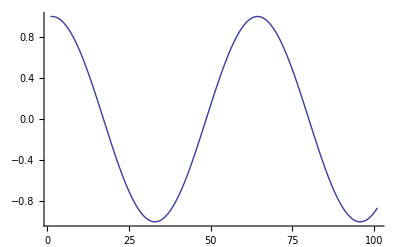

```mathematica
ListPlot[Transpose[sol][[2]],Joined->True]
```

That certainly looks like simple harmonic motion.
  
  The question asks us to plot velocity against position, so we need to compute the velocities. We know how to do this :
  v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt),
  a centred difference formula. We could just use the results already calculated, and post-process them to get the velocities, put the positions and velocities together, and plot them:

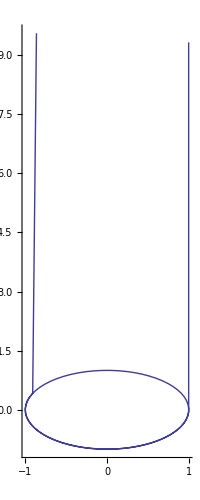

```mathematica
pos=Transpose[sol][[2]];
vel=(RotateLeft[pos]-RotateRight[pos])/(2 Δt);
ListPlot[Transpose[{pos,vel}],Joined->True,AspectRatio->Automatic]
```

Of course, the reason why this looks bad is that the Rotate functions have wrapped around, so we need to ignore the first and last entries :

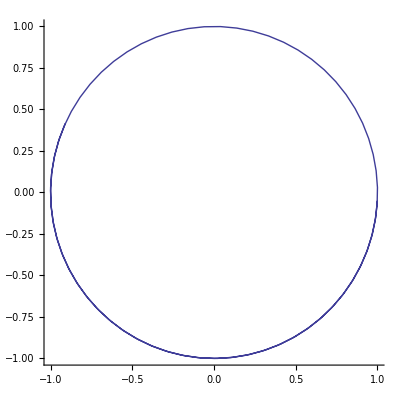

```mathematica
ListPlot[Rest[Most[Transpose[{pos,vel}]]],Joined->True,AspectRatio->Automatic]
```

Alternatively, we could add the velocity to the list of items calculated at each step (and, of course, to the initial values).

```mathematica
upd2[{xnext_,x_,v_}]:={2 xnext-x-Δt^2 xnext,xnext,((2 xnext-x-Δt^2 xnext)-x)/(2 Δt)}
init={1.,1.,0.}
upd2[init]
```

{1.,1.,0.}

{0.99,1.,-0.05}

Now the last two items in the list for each time step are the position and velocity at the same time (note that if we took the first and last we would have a time lag of Δt between the position and the speed).

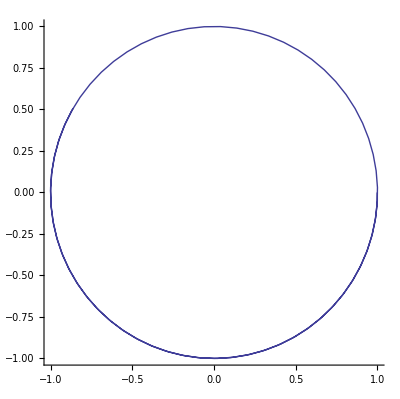

```mathematica
sol = NestList[upd2, init, 100]; 
  ListPlot[Map[Rest, sol], Joined -> True, 
   AspectRatio -> Automatic]
```

What has been done in the solution below is to take this scheme, and 
  1. modify the update function so that the time step is also an argument
  2. draw the unit circle and show it together with the phase plot
  3. add some titles to the graphs
  4. calculate the energy error from the results
  5. put all the statements together into a module (just to make it easy to repeat the calculation for different time steps).
  But there is nothing at all wrong with leaving the calculation as a set of individual commands and executing them more than once: the module is not essential.

## Solution

```mathematica
V[h_,t_]:=Module[{},updV[{xnext_,x_,v_},Δt_]:={2 xnext-x-Δt^2 xnext,xnext,((2 xnext-x-Δt^2 xnext)-x)/(2 Δt)};sol=NestList[updV[#1,h]&,{1.,1.,0.},Floor[t/h]];phasplot=ListPlot[Map[Rest,sol],Joined->True,PlotLabel->StringForm["Simple Verlet, Δt=``",h]];phasideal=Graphics[{RGBColor[1,0,0],Circle[{0.,0.},1.]}];Print[Show[phasplot,phasideal,AspectRatio->Automatic]];ListPlot[(0.5-1/2 Rest[#1].Rest[#1]&)/@sol,Joined->True,PlotLabel->StringForm["Simple Verlet, Δt=``",h]]]
```

```mathematica
lfV[h_,t_]:=Module[{},updlfV[{vhnext_,xnext_,v_},Δt_]:={vhnext-Δt xnext,xnext+Δt (vhnext-Δt xnext),1/2 (vhnext+(vhnext-Δt xnext))};sol=NestList[updlfV[#1,h]&,{0.,1.,0.},Floor[t/h]];sol=Transpose[sol];sol=Transpose[{Drop[sol⟦2⟧,-1],Rest[sol⟦3⟧]}];phasplot=ListPlot[sol,Joined->True];phasideal=Graphics[{RGBColor[1,0,0],Circle[{0.,0.},1.]}];Print[Show[phasplot,phasideal,AspectRatio->Automatic,PlotLabel->StringForm["Leapfrog Verlet, Δt=``",h]]];ListPlot[(0.5-(#1.#1)/2&)/@sol,Joined->True,PlotLabel->StringForm["Leapfrog Verlet, Δt=``",h]]]
```

```mathematica
vV[h_,t_]:=Module[{},updvV[{xnext_,vnext_},Δt_]:={xnext+Δt vnext-(Δt^2 xnext)/2,vnext-1/2 Δt ((xnext+Δt vnext-(Δt^2 xnext)/2)+xnext)};sol=NestList[updvV[#1,h]&,{1.,0.},Floor[t/h]];phasplot=ListPlot[sol,Joined->True];phasideal=Graphics[{RGBColor[1,0,0],Circle[{0.,0.},1.]}];Print[Show[phasplot,phasideal,AspectRatio->Automatic,PlotLabel->StringForm["Velocity Verlet, Δt=``",h]]];ListPlot[(0.5-(#1.#1)/2&)/@sol,Joined->True,PlotLabel->StringForm["Velocity Verlet, Δt=``",h]]]
```

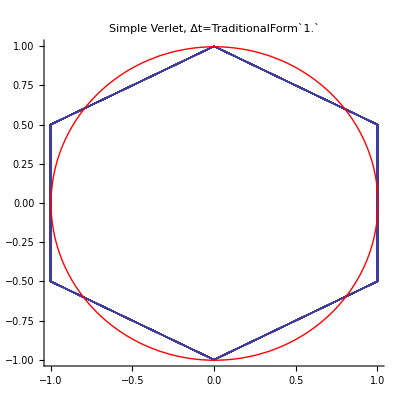

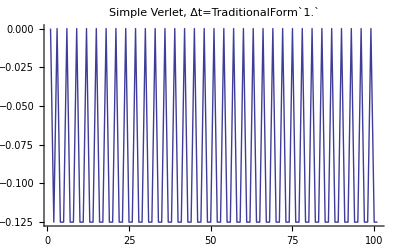

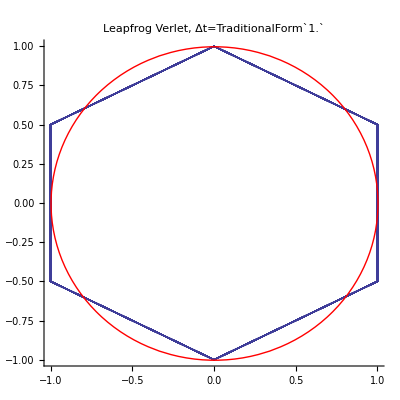

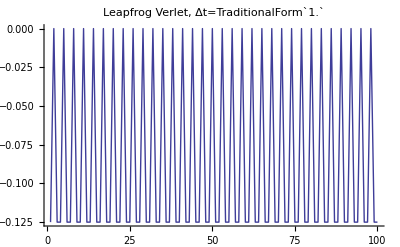

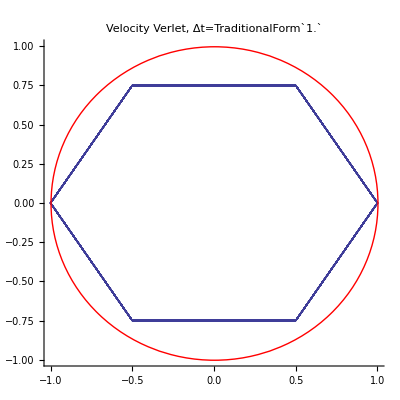

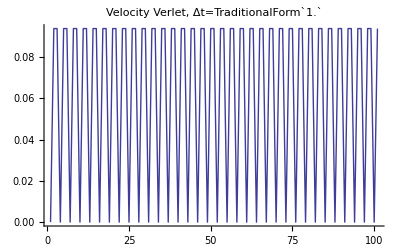

```mathematica
V[1.,100.]
lfV[1.,100.]
vV[1.,100.]
```

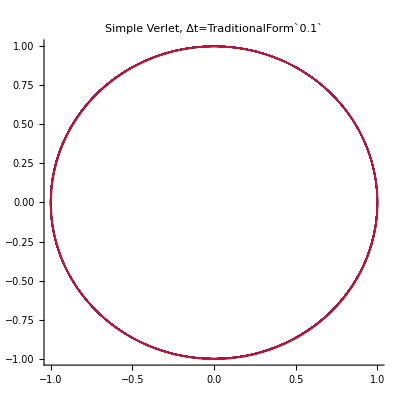

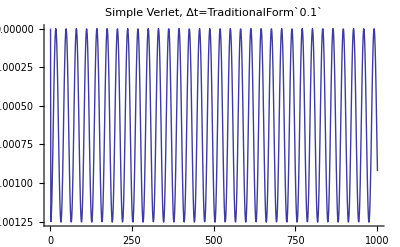

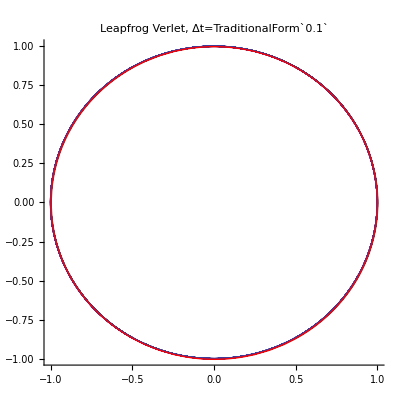

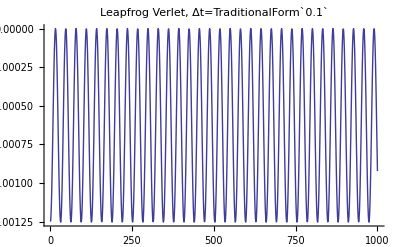

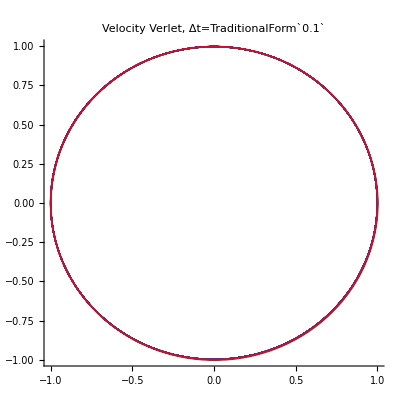

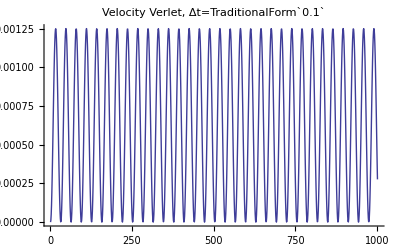

```mathematica
V[.1,100.]
lfV[.1,100.]
vV[.1,100.]
```

The crucial point to observe about all three algorithms is that there is no general drift of the energy as time progresses -- contrast this with the forward Euler method discussed in Lecture 3. The other point is that they seem identical when it comes to accuracy. Furthermore, even with a ridiculously long timestep they do not produce rubbish. If you want to do molecular dynamics (basically, particles interacting with potentials) a Verlet algorithm is the simple 'best buy'.

2. This question is one that requires pencil and paper rather than programming. It is concerned with the consistency of finite difference schemes.
  If we try to solve the equation
  (∂y)/(∂t)=(∂^2 y)/(∂x^2)
  with the simplest scheme we can think of, we might use a centred difference scheme for the time derivative and a standard scheme for the spatial second derivative. With x→i Δx and t→n Δt this gives
  (y(i,n+1)-y(i,n-1))/(2 Δt)= (y(i-1,n)-2y(i,n)+y(i+1,n))/(Δx)^2.
  Unfortunately, this scheme is unstable. Maybe it is possible to make it stable by inserting values of y at different times on the right-hand side. A fairly general way of doing this is to write
   (y(i,n+1)-y(i,n-1))/(2 Δt)= (y(i-1,n)-2[θ y(i,n+1) + (1-θ) y(i,n-1)]+y(i+1,n))/(Δx)^2.
   Investigate the consistency of this scheme as Δx tends to zero if:
   i) Δt = r Δ x
   ii) Δt = r (Δx)^2
   where r is a positive constant, and θ may take any value between 0 and 1.

Making Taylor expansions as usual, using the notation y_t to represent the first derivative with respect to time, and so on,
y(i+1,n)=y(i,n)+Δx y_x(i,n)+1/2(Δx)^2 y_xx(i,n)+1/6(Δx)^3 y_xxx(i,n)+...
y(i-1,n)=y(i,n)-Δx y_x(i,n)+1/2(Δx)^2 y_xx(i,n)-1/6(Δx)^3 y_xxx(i,n)+...
y(i,n+1)=y(i,n)+Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)+1/6(Δt)^3 y_ttt(i,n)+...
y(i,n-1)=y(i,n)-Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)-1/6(Δt)^3 y_ttt(i,n)+...
and substituting these values into the difference scheme gives

1/(2 Δ t)(y(i,n)+Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)+1/6(Δt)^3 y_ttt(i,n)+...-y(i,n)+Δt y_t(i,n)-1/2(Δt)^2 y_tt(i,n)+1/6(Δt)^3 y_ttt(i,n)+...)= 1/(Δ x)^2(y(i,n)+Δx y_x(i,n)+1/2(Δx)^2 y_xx(i,n)+1/6(Δx)^3 y_xxx(i,n)+...-2[θ {y(i,n)+Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)+1/6(Δt)^3 y_ttt(i,n)+...} + (1-θ) {y(i,n)-Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)-1/6(Δt)^3 y_ttt(i,n)+...}]+y(i,n)-Δx y_x(i,n)+1/2(Δx)^2 y_xx(i,n)-1/6(Δx)^3 y_xxx(i,n)+...)

with a bit of rearrangement,

1/(2 Δt)(2Δt y_t(i,n)+1/3(Δt)^3 y_ttt(i,n)+...)= 1/(Δ x)^2((Δx)^2 y_xx(i,n)+2/(4!)(Δx)^4 y_xxxx(i,n)+...-2[(2θ-1) Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)+(2θ-1)1/6(Δt)^3 y_ttt(i,n)])

so that, dropping the ...s

y_t(i,n)+1/6(Δt)^2 y_ttt(i,n)=  y_xx(i,n)+2/(4!)(Δx)^2 y_xxxx(i,n)+...-2/(Δx)^2[(2θ-1) Δt y_t(i,n)+1/2(Δt)^2 y_tt(i,n)+(2θ-1)1/6(Δt)^3 y_ttt(i,n)]

or, keeping only the lower orders of small quantities,

{y_t(i,n)-y_xx(i,n)}+{1/6(Δt)^2 y_ttt(i,n)  -2/(4!)(Δx)^2 y_xxxx(i,n)+(2θ-1)  (2Δt)/(Δx)^2 y_t(i,n)+(Δt)^2/(Δx)^2 y_tt(i,n)}=0.

Now we can see that as long as the second curly bracket tends to zero, the result tends to the differential equation 
  y_t(i,n)-y_xx(i,n)=0.

Now consider the special cases:
      i) Δ t = r Δ x:
      as Δx tends to zero the second bracket becomes
      {(2θ-1)  (2r)/Δx y_t(i,n)+r^2 y_tt(i,n)}.
      Now we are in trouble: if θ≠1/2, the first term tends to infinity as Δx tends to zero.  In this case, the finite difference system is unstable for any value of r.
      If, on the other hand, θ=1/2, we have an extra term which does not go to zero and the differential equation we solve with the difference scheme is actually
       y_t-y_xx+r^2 y_tt=0.
       ii) Δt = r (Δx)^2
       Now the second bracket becomes
        2(2θ-1)  r y_t(i,n)
        which avoids the instability of method i), but tells us that the differential equation we are solving is
        (1+(2θ-1))y_t-y_xx=0,
        which is only equal to the equation we want if we choose θ=1/2.
        This exercise illustrates the fact that the issue of consistency is non-trivial, and that arbitrary selection of a difference scheme may lead to a procedure that is well-behaved, but which does not solve the intended differential equation.

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.